```mathematica
(* The Empirical Definition of Probability *)
```

```mathematica
Clear[t, t2, t3]
```

```mathematica
(* Toss a coin n times and count the running proportion of tails to the running total number of throws *)
t2 = RandomChoice[{0.5, 0.5} -> {head, tail}, 10000];
```

```mathematica
pt = Divide[Count[#,tail], N[Length[#]]] & /@ Table[Take[t2, i], {i, 1, 10000}];
```

```mathematica
(* Check out the last few probabilities for tails *)
Take[pt, -10]
```

{0.49955,0.4995,0.49955,0.4996,0.49955,0.4996,0.49955,0.4996,0.49965,0.4997}

```mathematica
(* pretty close to 0.5! *)
```

```mathematica
cHalf = Table[0.5, {10000}];
```

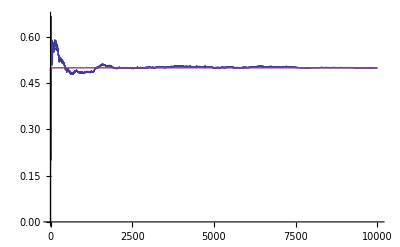

```mathematica
ListLinePlot[{pt, cHalf}, PlotRange-> All, AspectRatio->1/GoldenRatio]
```

```mathematica
(* n people playing Russian Roulette, once a year *)
(* How many years will a person live? What is the probability? *)
```

{0.,0.195272,0.14594,0.107914,0.100719,0.0688592,0.0554985,0.0626927,0.045221,0.0462487,0.0267215,0.0318602,0.0154162,0.0215827,0.0195272,0.0143885,0.012333,0.0102775,0.0102775,0.00822199,0.00102775}

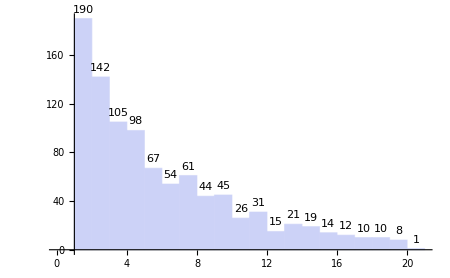

```mathematica
r = Table[RandomChoice[{5/6., 1/6.} -> {b,h},20], {1000}];
fr = DeleteCases[Flatten[If[Length[a = Position[#,h]] > 0, First[a], 0] & /@ r],0];
bfr = BinCounts[fr];
pfr = N[#/Total[bfr]] & /@ bfr (* probability of dying in year n *)
cfr = Histogram[fr, {1}, LabelingFunction->Above, ImageSize->450]
```

```mathematica
pd = PoissonDistribution[10];
```

```mathematica
PDF[pd, 4] // N
```

0.0189166

```mathematica
PDF[pd, 6] // N
```

0.0630555

```mathematica
CDF[pd,1] // N
```

0.000499399

```mathematica
RandomChoice[{PDF[pd,4], CDF[pd,6]} -> {b, h}, 5]
```

{h,h,h,h,h}

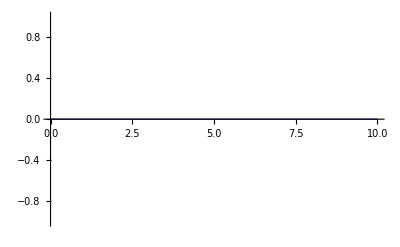

```mathematica
Plot[PDF[pd, x], {x, 0,10}]
```

```mathematica
t = N[PDF[pd, #]]& /@ Range[10]
```

{0.000453999,0.00227,0.00756665,0.0189166,0.0378333,0.0630555,0.0900792,0.112599,0.12511,0.12511}

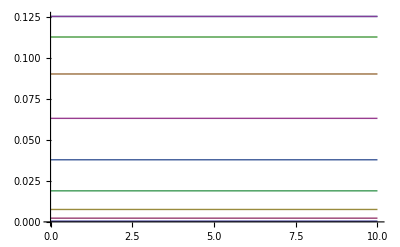

```mathematica
Plot[t, {x, 0,10}]
```

```mathematica
(* RED BLACK GAMES *)
startAmt = 100; (* initial amount *)
needAmt = 200; (* amount needed to win and quit *)

betAmt[needAmt_, currentAmt_, bet_]:= Module[{},
(* This is the betting strategy *)
(* The needAmt is ignored in this strategy where a fixed amount is bet every time (subject to the conditions below) *)
Which[currentAmt ≤ 0, 0, currentAmt < bet, currentAmt, currentAmt > bet, bet]
];
betAmt2[needAmt_, currentAmt_, bet_]:= Module[{},
(* This is an alternative betting strategy *)
(* The fixed bet is ignored in this version of the strategy *)
Which[currentAmt ≤ 0,0,
 (needAmt- currentAmt) ≤ currentAmt, needAmt - currentAmt, 
(needAmt- currentAmt) > currentAmt, currentAmt]
];

state[currentAmt_, outcome_, bet_, needAmt_]:= Module[{out},
(* Determine what the bet should be *)
b = betAmt2[needAmt,currentAmt, bet];
If[outcome == 1, out = currentAmt + bet, out = currentAmt - bet];
out
];
```

```mathematica
genGames[p1_, p0_, nLength_, nTrials_]:= Module[{},
(* Generates nTrials number of games, each of length nLength with probability of success = p1 and probability of failure = p0 *)
Table[RandomChoice[{p1,p0} -> {1, 0}, nLength], {nTrials}]
];
```

```mathematica
trials = genGames[0.3, 0.7, 10, 3]
```

{{0,0,1,0,0,0,0,0,0,1},{0,0,0,1,0,1,1,0,1,0},{0,1,0,0,0,1,0,0,1,0}}

```mathematica
gameResult[game_, startAmt_, needAmt_, bet_]:= Module[{r, res, n, zeros, wins, out},
(* Calculate the current amount from one play of the game to the next *)
r[1] = state[startAmt, game[[1]], bet, needAmt];
r[n_] := state[r[n-1],game[[n]], bet, needAmt];
res = Table[r[i], {i,1,Length[game]}];
zeros = Flatten[Position[res, x_ /; x ≤ 0]];
firstZero = If[Length[zeros] > 0, First[zeros], "no bankruptcy"];
wins = Flatten[Position[res, x_ /; x ≥  needAmt]];
firstWin =If[Length[wins] > 0, First[wins], "no win"];
(* There are 4 cases *)
out = {firstZero, firstWin};
Which[IntegerQ[firstZero] && IntegerQ[firstWin] && firstZero < firstWin, {"Bankrupt on play", firstZero},
IntegerQ[firstZero] && IntegerQ[firstWin] && firstZero > firstWin, {"Win on play", firstWin},
IntegerQ[firstZero] && firstWin == "no win", {"Bankrupt on play", firstZero},
firstZero == "no bankruptcy" && IntegerQ[firstWin], {"Win on play", firstWin},
firstZero == "no bankruptcy" && firstWin == "no win", {"Leave with current amount", r[Length[game]]}]
];
```

```mathematica
g = genGames[0.5, 0.5, 100, 30];
```

```mathematica
gr = gameResult[#, 50, 100, 20] & /@ g
```

{{Bankrupt on play,5},{Win on play,19},{Win on play,29},{Win on play,15},{Bankrupt on play,5},{Win on play,3},{Bankrupt on play,5},{Bankrupt on play,29},{Bankrupt on play,3},{Bankrupt on play,5},{Win on play,13},{Bankrupt on play,5},{Bankrupt on play,3},{Win on play,9},{Bankrupt on play,21},{Bankrupt on play,13},{Win on play,3},{Win on play,7},{Bankrupt on play,5},{Win on play,3},{Win on play,11},{Win on play,19},{Win on play,11},{Win on play,5},{Bankrupt on play,3},{Bankrupt on play,7},{Bankrupt on play,3},{Bankrupt on play,7},{Win on play,3},{Win on play,7}}

```mathematica
(* How many plays till you're bankrupt? *)
```

```mathematica
bankrupt = Sort[Tally[gr[[All, 1]]], #1[[2]]> #2[[2]] &]
```

{{4,5},{2,2},{14,1},{10,1},{6,1}}

```mathematica
(* How many plays till you win? *)
win = Sort[Tally[gr[[All, 2]]], #1[[2]]> #2[[2]] &]
```

{{no win,7},{12,1},{2,1},{6,1}}